```mathematica
pp1 = Import["C:\\Users\\Миша\\source\\repos\\mymath2\\mymath2\\shod1.txt", "Table"];
```

```mathematica
xyN = Transpose@((Transpose@pp1)[[1;;2]]);
ts  = (Transpose@pp1)[[3]];
```

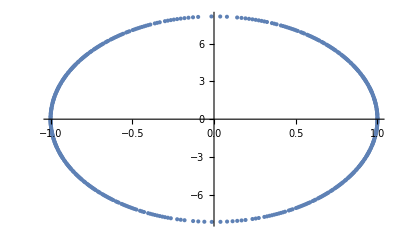

```mathematica
ListPlot[xyN]
```

```mathematica
DSolve[{u1'[t]==u2[t], u2'[t] == -200/3 u1[t], u1[0]==1, u2[0]==0}, {u1[t], u2[t]}, t]
```

{{u1[t]→Cos[10 √(2/3) t],u2[t]→-10 √(2/3) Sin[10 √(2/3) t]}}

```mathematica
err=Table[{1 - Abs[(- el[[1]])/Cos[10 √(2/3) el[[3]]]] , 1-Abs[el[[2]]/10 √(2/3) Sin[10 √(2/3) el[[3]]] ]}, {el, pp1}];
```

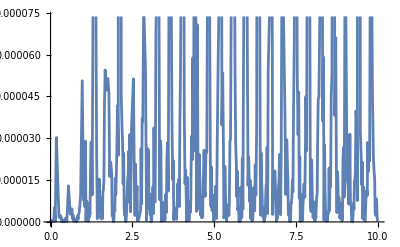

```mathematica
ListLinePlot[Transpose@{ts,(Transpose@err)[[1]]}]
```

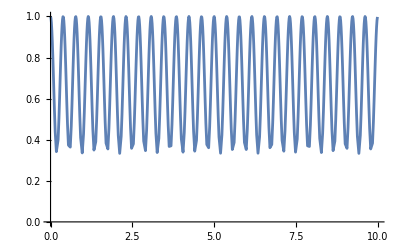

```mathematica
ListLinePlot[Transpose@{ts,(Transpose@err)[[2]]}]
```

```mathematica
Max[err]
```

1

```mathematica
Mean[err]
```

{0.0000299182,0.753749}